```mathematica
uCA = 0.025*M^0.860;
uCO= 0.029*M^0.919;
uNRF = 0.030*M^0.881;
uRF = 0.041*M^0.897;
```

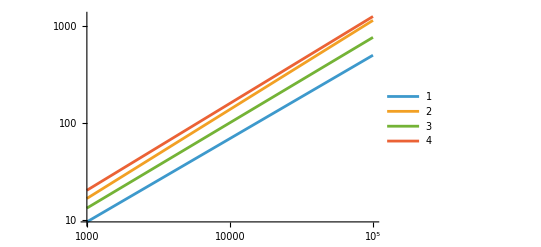

```mathematica
LogLogPlot[{uCA,uCO,uNRF,uRF},{M,10^3,10^5},PlotLegends->Automatic]
```

```mathematica
uMax = uRF;
uMin = uCA;
```

```mathematica
FullSimplify[uMax/uMin]
```

1.64 M^0.037

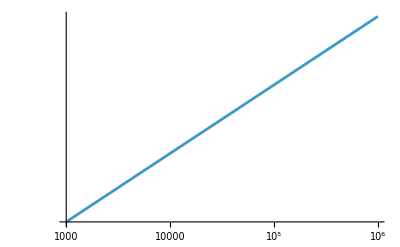

```mathematica
LogLogPlot[uMax/uMin,{M,10^3,10^6}]
```

```mathematica
N[uMax/uMin]/.M->900
```

2.10936

```mathematica
N[uMax/uMin]/.M->100
```

1.94466